# Cuaderno de Prácticas

## Álgebra

## Grado en Ingeniería Informática

## CURSO 2025/26

## Datos personales

Nombre y apellidos : Francisco Javier Martín - Lunas Escobar
DNI : 26268082
Grupo de teoría : A
Grupo de prácticas :1

## Práctica 5

```mathematica
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.1 *)
MATRIZADYACENCIA[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1;
matrizadyacencia[[nuevoF[[k,2]],nuevoF[[k,1]]]]=1;
,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 2.2. Matriz de adyacencia - Función 5.2 *)
MATRIZADYACENCIADIR[W_,F_]:=Module[{k,i,j,CONTADORi,nuevoF},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizadyacencia=Table[0,{i,Length[W]},{j,Length[W]}];
Do[matrizadyacencia[[nuevoF[[k,1]],nuevoF[[k,2]]]]=1,{k,Length[F]}];
matrizadyacencia];
(* Cap 5 - 4 Grafos Isomorfos - Función 5.10 *)
ISOMORFOS[A1_,A2_]:=Module[{matricesP,i,j},
Isomorfos=False;
If[Dimensions[A1]==Dimensions[A2],   
matricesP=Permutations[IdentityMatrix[Dimensions[A1][[1]]]];   
Do[	      
If[matricesP[[i]].A1.Transpose[matricesP[[i]]]==A2,
Isomorfos=True;matrizP=matricesP[[i]];permutacion=i;Break[];];
   ,{i,Length[matricesP]}];
];

If[Isomorfos,
Print["Son isomorfos, una matriz P es: ",MatrixForm[matrizP], 
      ", una permutación es: ",
MatrixForm[{Table[j,{j,Dimensions[A1][[1]]}],Permutations[Table[j,{j,Dimensions[A1][[1]]}]][[permutacion]]}]]
,Print["No son isomorfos"]];
];
(**)
```

```mathematica
(* Cap 5 - 2.2. Matriz de incidencia - Función 5.5 *)
MATRIZINCIDENCIA[W_,F_]:=Module[{i,j,nuevoF,CONTADORi},
nuevoF={};
Do[AppendTo[nuevoF,Position[W,F[[CONTADORi]][[1]]][[1]][[1]]->Position[W,F[[CONTADORi]][[2]]][[1]][[1]]];
,{CONTADORi,Length[F]}];
matrizincidencia=Table[0,{i,Length[W]},{j,Length[F]}];
Do[Do[
matrizincidencia[[nuevoF[[j]][[i]],j]]=1;
,{i,2}];,{j,Length[F]}];
matrizincidencia
];
```

```mathematica
(* Sesión 5 cap 6 *)
<<"Combinatorica`";
BIPARTITO[W_,F_]:=Module[{i,subconjuntos,j,fin},
bipartito=False;
i=1;
fin=Quotient[Length[W],2];
While[!bipartito && i<=fin,
subconjuntos=KSubsets[W,i];
j=1;
While[!bipartito && j<=Length[subconjuntos],
If[IND[subconjuntos[[j]],F]=={},
If[IND[Complement[W,subconjuntos[[j]]],F]=={},
bipartito=True;
W1=subconjuntos[[j]];
W2=Complement[W,subconjuntos[[j]]];
];
];
j++;];
i++;];
If[bipartito,Print["Es bipartito: W1=",W1," y W2=",W2];
If[Length[F]==Length[W1]*Length[W2],Print["Es bipartito completo: ",Subscript["K", Length[W1],Length[W2]]  ], Print["No es bipartito completo"]];
,Print["No es bipartito"]];
]
(* Sesión 5 cap 6 *)
REGULAR[matrizadyacencia_]:=Module[{i,j},
grado=Sum[matrizadyacencia[[1,j]],{j,Dimensions[matrizadyacencia][[1]]}];
regular=True;
Do[
If[grado!=Sum[matrizadyacencia[[i,j]],{j,1,Dimensions[matrizadyacencia][[1]]}],regular=False;Break[];];
,{i,2,Dimensions[matrizadyacencia][[1]]}];
regular
];
(* Sesión 5 cap 6 *)
COMPLETO[matrizadyacencia_]:=   (Sum[MatrixPower[matrizadyacencia,2][[i,i]],{i,Dimensions[matrizadyacencia][[1]]}]==Dimensions[matrizadyacencia][[1]]*(Dimensions[matrizadyacencia][[1]]-1))
```

General::compat: Combinatorica Graph and Permutations functionality has been superseded by preloaded functionality. The package now being loaded may conflict with this. Please see the Compatibility Guide for details.

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

### Ejercicio 2 Calcular conjunto de vértices y lados, matriz de adyacencia, matriz de incidencia y representación gráfica de los grafos del ejercicio 6.8 del manual de prácticas

#### a) -Graphics-

```mathematica
WEjer2GIa={1,2,3,4,5,6};
FEjer2GIa={1->2,3->1,4->5,6->1}

"MATRIZADYACENCIA"
AEjer2GIa=MATRIZADYACENCIA[WEjer2GIa,FEjer2GIa];
AEjer2GIa//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIa=MATRIZINCIDENCIA[WEjer2GIa,FEjer2GIa];
IEjer2GIa//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIa;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"¿Es completo?"
COMPLETO[AEjer2GIa]
"¿Es regular?"
REGULAR[AEjer2GIa]
"¿Es bipartito?"
BIPARTITO[WEjer2GIa,FEjer2GIa]
```

{1→2,3→1,4→5,6→1}

MATRIZADYACENCIA

(0 | 1 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)

MATRIZINCIDENCIA

(1 | 1 | 0 | 1
1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6}

{2→1,3→1,6→1,1→2,1→3,5→4,4→5,1→6}

¿Es completo?

False

¿Es regular?

False

¿Es bipartito?

No es bipartito

#### b)-Graphics-

```mathematica
matrizadyacenciaEjer2GIb=({{0, 1, 0, 1}, {1, 0, 1, 0}, {0, 1, 0, 1}, {1, 0, 1, 0}});
Wb=Table[i,{i,Dimensions[matrizadyacenciaEjer2GIb]⟦1⟧}]
Fb={};
Do[Do[If[matrizadyacenciaEjer2GIb⟦i,j⟧==1,AppendTo[Fb,i->j]];,{i,j}];
,{j,Dimensions[matrizadyacenciaEjer2GIb]⟦1⟧}];
Fb
```

{1,2,3,4}

{1→2,2→3,1→4,3→4}

```mathematica
WEjer2GIb={1,2,3,4};
FEjer2GIb={1->2,2->3,1->4,3->4};
"MATRIZINCIDENCIA"
IEjer2GIb=MATRIZINCIDENCIA[WEjer2GIb,FEjer2GIb];
IEjer2GIb//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}]
F={};
Do[Do[If[matrizadyacenciaEjer2GIb[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];,{j,Dimensions[matrizadyacenciaEjer2GIb][[1]]}];
F
"¿Es completo?"
COMPLETO[matrizadyacenciaEjer2GIb]
"¿Es regular?"
REGULAR[matrizadyacenciaEjer2GIb]
"¿Es bipartito?"
BIPARTITO[WEjer2GIb,FEjer2GIb]
```

MATRIZINCIDENCIA

(1 | 0 | 1 | 0
1 | 1 | 0 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1)

Vertices y lados

{1,2,3,4}

{2→1,4→1,1→2,3→2,2→3,4→3,1→4,3→4}

¿Es completo?

False

¿Es regular?

True

¿Es bipartito?

No es bipartito

#### c)-Graphics-

```mathematica
matrizincidenciaEjer2GIc=({{1, 1, 0, 0, 0, 0}, {0, 0, 1, 1, 0, 0}, {0, 0, 0, 0, 1, 1}, {1, 0, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 1}});

W=Table[i,{i,Dimensions[matrizincidenciaEjer2GIc][[1]]}]
F={};
Do[
AppendTo[F,Position[Transpose[matrizincidenciaEjer2GIc][[i]],1][[1]][[1]]->Position[Transpose[matrizincidenciaEjer2GIc][[i]],1][[2]][[1]]]
,{i,Dimensions[matrizincidenciaEjer2GIc][[2]]}];
F
```

{1,2,3,4,5}

{1→4,1→5,2→4,2→5,3→4,3→5}

```mathematica
WEjer2GIc={1,2,3,4,5};
FEjer2GIc={1->4,1->5,2->4,2->5,3->4,3->5};
"MATRIZADYACENCIA"
AEjer2GIc=MATRIZADYACENCIA[WEjer2GIc,FEjer2GIc];
AEjer2GIc//MatrixForm
"Vertices y lados"
W=Table[i,{i,Dimensions[AEjer2GIc][[1]]}]
F={};
Do[Do[If[AEjer2GIc[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[AEjer2GIc][[1]]}];,{j,Dimensions[AEjer2GIc][[1]]}];
F
"¿Es completo?"
COMPLETO[AEjer2GIc]
"¿Es regular?"
REGULAR[AEjer2GIc]
"¿Es bipartito?"
BIPARTITO[WEjer2GIc,FEjer2GIc]
```

MATRIZADYACENCIA

(0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 1 | 1
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0)

Vertices y lados

{1,2,3,4,5}

{4→1,5→1,4→2,5→2,4→3,5→3,1→4,2→4,3→4,1→5,2→5,3→5}

¿Es completo?

False

¿Es regular?

False

¿Es bipartito?

No es bipartito

#### d)-Graphics-

```mathematica
"Hacer el ejercicio que falta, g5"
```

```mathematica
"d"
WEjer2GIdg4={1,2,3,4,5,6,7,8};
FEjer2GIdg4={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,1},{1,4},{2,7},{3,6},{5,8}}
"MATRIZADYACENCIA"
AEjer2GIdg4=MATRIZADYACENCIA[WEjer2GIdg4,FEjer2GIdg4];
AEjer2GIdg4//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIdg4=MATRIZINCIDENCIA[WEjer2GIdg4,FEjer2GIdg4];
IEjer2GIdg4//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIdg4;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"¿Es completo?"
COMPLETO[AEjer2GIdg4]
"¿Es regular?"
REGULAR[AEjer2GIdg4]
"¿Es bipartito?"
BIPARTITO[WEjer2GIdg4,FEjer2GIdg4]
```

d

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,1},{1,4},{2,7},{3,6},{5,8}}

MATRIZADYACENCIA

(0 | 1 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1 | 0 | 0
1 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

MATRIZINCIDENCIA

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1)

Vertices y lados

{1,2,3,4,5,6,7,8}

{2→1,4→1,8→1,1→2,3→2,7→2,2→3,4→3,6→3,1→4,3→4,5→4,4→5,6→5,8→5,3→6,5→6,7→6,2→7,6→7,8→7,1→8,5→8,7→8}

¿Es completo?

False

¿Es regular?

True

¿Es bipartito?

No es bipartito

```mathematica
WEjer2GIdg5={1,2,3,4};
FEjer2GIdg5={{1,2},{2,3},{3,1},{1,4},{2,4},{3,4}}
"MATRIZADYACENCIA"
AEjer2GIdg5=MATRIZADYACENCIA[WEjer2GIdg5,FEjer2GIdg5];
AEjer2GIdg5//MatrixForm
"MATRIZINCIDENCIA"
IEjer2GIdg5=MATRIZINCIDENCIA[WEjer2GIdg5,FEjer2GIdg5];
IEjer2GIdg5//MatrixForm
"Vertices y lados"
matrizadyacencia=AEjer2GIdg5;
W=Table[i,{i,Dimensions[matrizadyacencia][[1]]}]
F={};
Do[Do[If[matrizadyacencia[[i,j]]==1,AppendTo[F,i->j]];,{i,Dimensions[matrizadyacencia][[1]]}];,{j,Dimensions[matrizadyacencia][[1]]}];
F
"¿Es completo?"
COMPLETO[AEjer2GIdg5]
"¿Es regular?"
REGULAR[AEjer2GIdg5]
"¿Es bipartito?"
BIPARTITO[WEjer2GIdg5,FEjer2GIdg5]
```

{{1,2},{2,3},{3,1},{1,4},{2,4},{3,4}}

MATRIZADYACENCIA

(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)

MATRIZINCIDENCIA

(1 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 0
0 | 1 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 1)

Vertices y lados

{1,2,3,4}

{2→1,3→1,4→1,1→2,3→2,4→2,1→3,2→3,4→3,1→4,2→4,3→4}

¿Es completo?

True

¿Es regular?

True

¿Es bipartito?

No es bipartito

### Ejercicio 2 Estudiar si el grafo del ejercicio 3 de la convocatoria ordinaria 2 del curso 2023/24, es regular, completo, bipartito y/o bipartito completo. Análogamente para in octógono K6 y K4,3.

#### -Graphics-

```mathematica
WEjerGIdg1={1,2,3,4,5,6};
FEjerGIdg1={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,4},{2,5},{3,6}}
"MATRIZADYACENCIA"
AEjerGIdg1=MATRIZADYACENCIA[WEjerGIdg1,FEjerGIdg1];
AEjerGIdg1//MatrixForm
"¿Es completo?"
COMPLETO[AEjerGIdg1]
"¿Es regular?"
REGULAR[AEjerGIdg1]
"¿Es bipartito?"
BIPARTITO[WEjerGIdg1,FEjerGIdg1]
```

{{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{1,4},{2,5},{3,6}}

MATRIZADYACENCIA

(0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0
0 | 1 | 0 | 1 | 0 | 1
1 | 0 | 1 | 0 | 1 | 0)

¿Es completo?

False

¿Es regular?

True

¿Es bipartito?

No es bipartito

#### Octógono

MATRIZADYACENCIA

(0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 0)

¿Es completo?

True

¿Es regular?

True

¿Es bipartito?

No es bipartito

Representacion gráfica

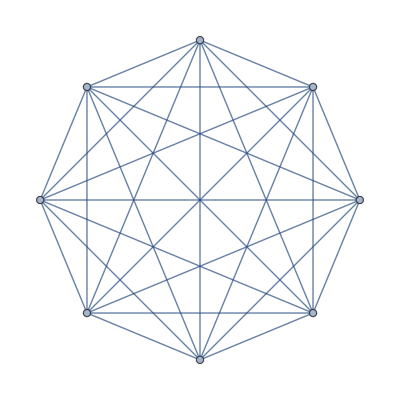

```mathematica
WEjerGIdg2=Range[8];;
FEjerGIdg2=Subsets[WEjerGIdg2, {2}];
"MATRIZADYACENCIA"
AEjerGIdg2=MATRIZADYACENCIA[WEjerGIdg2,FEjerGIdg2];
AEjerGIdg2//MatrixForm
"¿Es completo?"
COMPLETO[AEjerGIdg2]
"¿Es regular?"
REGULAR[AEjerGIdg2]
"¿Es bipartito?"
BIPARTITO[WEjerGIdg2,FEjerGIdg2]
"Representacion gráfica"
GraphPlot[AEjerGIdg2]
```

#### K6

MATRIZADYACENCIA

(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 0)

¿Es completo?

True

¿Es regular?

True

¿Es bipartito?

No es bipartito

Representacion gráfica

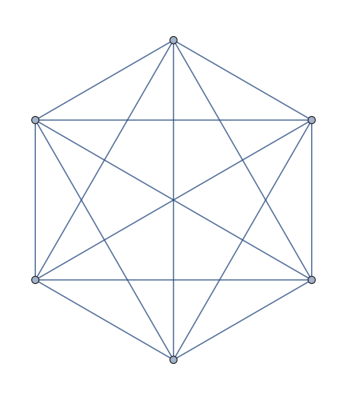

```mathematica
WEjerGIdg3=Range[6];
FEjerGIdg3=Subsets[WEjerGIdg3, {2}];
"MATRIZADYACENCIA"
AEjerGIdg3=MATRIZADYACENCIA[WEjerGIdg3,FEjerGIdg3];
AEjerGIdg3//MatrixForm
"¿Es completo?"
COMPLETO[AEjerGIdg3]
"¿Es regular?"
REGULAR[AEjerGIdg3]
"¿Es bipartito?"
BIPARTITO[WEjerGIdg3,FEjerGIdg3]
"Representacion gráfica"
GraphPlot[AEjerGIdg3]
```

#### K4,3

(0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 0 | 0)

¿Es completo?

False

¿Es regular?

False

¿Es bipartito?

No es bipartito

Representacion gráfica

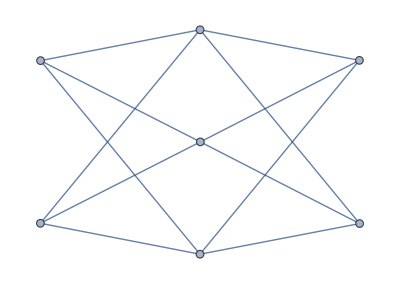

```mathematica
WEjerGIdg4 = {1,2,3,4,5,6,7};

A = {1,2,3,4};
B = {5,6,7};

FEjerGIdg4 = Flatten[
   Table[{i,j}, {i,A}, {j,B}],
   1
];

"MATRIZ ADYACENCIA";
AEjerGIdg4 = MATRIZADYACENCIA[WEjerGIdg4, FEjerGIdg4];
AEjerGIdg4 // MatrixForm

"¿Es completo?"
COMPLETO[AEjerGIdg4]

"¿Es regular?"
REGULAR[AEjerGIdg4]

"¿Es bipartito?"
BIPARTITO[WEjerGIdg4, FEjerGIdg4]

"Representacion gráfica"
GraphPlot[AEjerGIdg4]
```